```mathematica
(*r40Turb=Import["C:\\Users\\Sam\\Documents\\MATLAB\\KolmogorovDefects\\src\\R40_turbulent_state_k1.mat"][[2]];*)
(* Transpose because Matlab stores it transposed. Confirm that this is correct by having Div near zero everywhere *)
r40Turb=Transpose@Uncompress[mydata];
r40Turb//TensorDimensions//EchoLabel["Size of input data"];
ifunx=ListInterpolation[r40Turb[[;;,;;,1]],{{0,2Pi},{0,2Pi}}];
ifuny=ListInterpolation[r40Turb[[;;,;;,2]],{{0,2Pi},{0,2Pi}}];
dom=Rectangle[{0,0},{2Pi,2Pi}];
interpU[x_,y_]={ifunx[x,y],ifuny[x,y]};
divergenceOfU[x_,y_]=Div[interpU[x,y],{x,y}];
NIntegrate[Chop[Abs@divergenceOfU[x,y],0.01],{x,y}∈dom,AccuracyGoal->3]//EchoLabel["Total divergence of this thing is near zero"];
```

Size of input data  {128,128,2}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Total divergence of this thing is near zero  0.0061777

```mathematica
extSize=Pi/2;
extDomain=Rectangle[{-extSize,-extSize},{2Pi+extSize,2Pi+extSize}];
extPeriodicU[x_,y_]=interpU[Mod[x,2Pi],Mod[y,2Pi]];
```

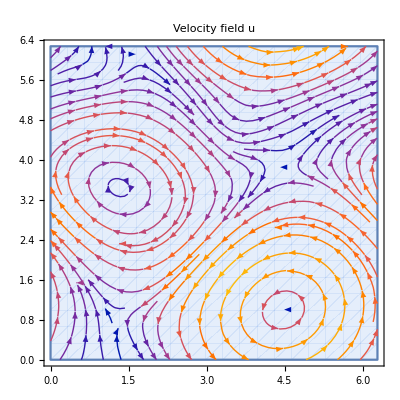

```mathematica
StreamPlot[interpU[x,y],{x,y}∈dom,PlotLabel->"Velocity field u"]
StreamPlot[extPeriodicU[x,y],{x,y}∈extDomain,PlotLabel->"Velocity field u (extended)"];
```

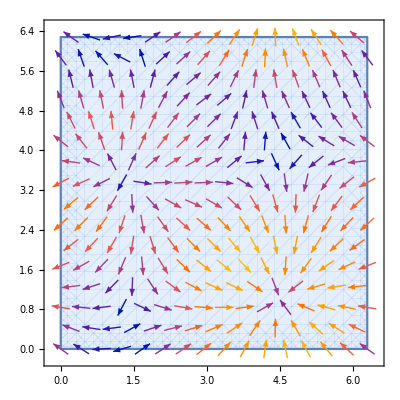

-Graphics3D-

```mathematica
skewU[x_,y_]={-ifuny[x,y],ifunx[x,y]};
VectorPlot[skewU[x,y],{x,y}∈dom]
Plot3D[Div[skewU[x,y],{x,y}]//Evaluate,{x,y}∈dom]
```

```mathematica
Clear[getStreamFuncInt]
getStreamFuncInt[u_]:=getStreamFuncInt[u]=Function[{x,y},NIntegrate[u[t x,0][[1]],{t,0,1}]+NIntegrate[u[x,t y][[2]],{t,0,1}]]
antiGradient[u_]:=NDSolveValue[{Laplacian[stream[x,y],{x,y}]-Curl[u[x,y],{x,y}]==0,stream[0,y]==stream[2Pi,y],stream[x,0]==stream[x,2Pi]},stream[x,y],{x,y}∈dom,Method->{"TimeIntegration"->{"Projection","Invariants"->Grad[stream[x,y],{x,y}]-u[x,y]}}]
getStreamFuncCurl[u_]:=NDSolveValue[{PoissonPDEComponent[{stream[x,y],{x,y}},<|"PoissonSourceTerm"->Curl[u[x,y],{x,y}]|>]==NeumannValue[0,True]},stream[x,y],{x,y}∈dom]
getStreamFuncCurl[interpU];
Plot3D[%//Evaluate,{x,y}∈dom]
```

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {stream}; the result may not be unique.

LinearSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolveValue::fempsf: PDESolve could not find a solution.

NDSolveValue::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {stream}; the result may not be unique.

LinearSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolveValue::fempsf: PDESolve could not find a solution.

NDSolveValue::dsvar: True cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics3D-

```mathematica
detdel[x_,y_]=D[ifunx[x,y],x]D[ifuny[x,y],y]-D[ifunx[x,y],y]D[ifuny[x,y],x];
vort[x_,y_]=Curl[{ifunx[x,y],ifuny[x,y],0},{x,y,z}][[3]];
Plot3D[detdel[x,y],{x,0,2Pi},{y,0,2Pi}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Max[detdel[x,y],a],{x,0,2Pi},{y,0,2Pi},PlotRange->{-3,6}],{a,-3,6}]
```

```mathematica
homologyPlot[phi_]:=Manipulate[Plot3D[phi,{x,0,2Pi},{y,0,2Pi},PlotRange->All,ColorFunction->Function[{x,y,z},Opacity[If[z<a,1,0.1],Green]],MeshFunctions->{#3&},Mesh->50],{a,0,1,0.01}]
```

```mathematica
Manipulate[Plot3D[vort[x,y],{x,0,2Pi},{y,0,2Pi},PlotRange->All,ColorFunction->Function[{x,y},Opacity[If[vort[x,y]<a,1,0.1],If[vort[x,y]<a,Red,Green]]],ColorFunctionScaling->False,MeshFunctions->{#3&},Mesh->50],{a,-5,10,0.01}]
```

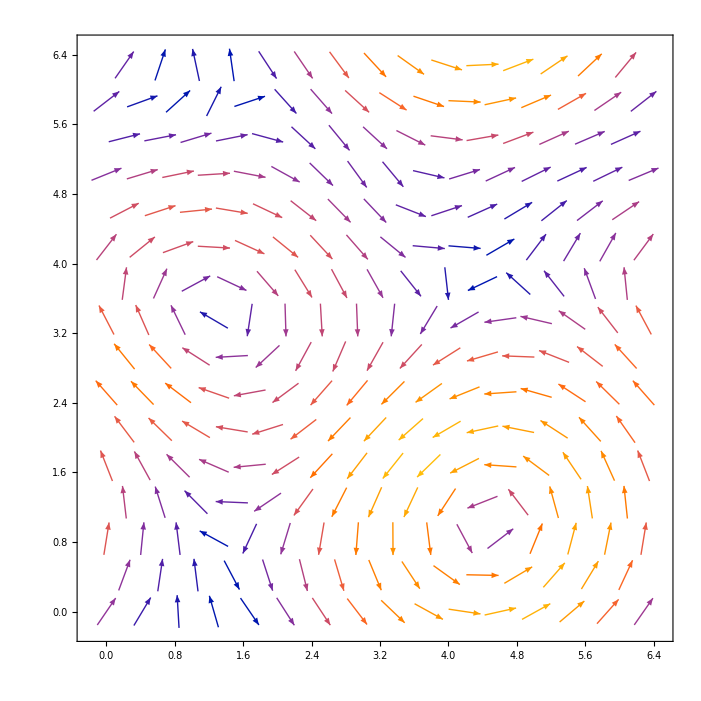

```mathematica
VectorPlot[{ifunx[x,y],ifuny[x,y]},{x,0,2Pi},{y,0,2Pi}]
```

```mathematica
Plot3D[Div[{ifunx[x,y],ifuny[x,y]},{y,x}]//Evaluate,{x,0,2Pi},{y,0,2Pi}]
Plot3D[Curl[{ifunx[x,y],ifuny[x,y],0},{y,x,z}][[3]]//Evaluate,{x,0,2Pi},{y,0,2Pi}]
```

-Graphics3D-

-Graphics3D-

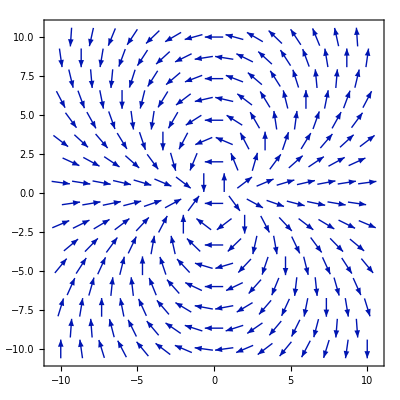

-Graphics3D-

```mathematica
VectorPlot[{Cos[2 ToPolarCoordinates[{x,y}][[2]]],Sin[2 ToPolarCoordinates[{x,y}][[2]]]},{x,-10,10},{y,-10,10}]
Plot3D[Norm@{Cos[2 ToPolarCoordinates[{x,y}][[2]]],Sin[2 ToPolarCoordinates[{x,y}][[2]]]},{x,-10,10},{y,-10,10}]
```

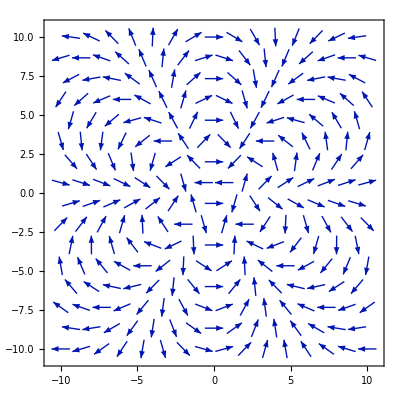

```mathematica
VectorPlot[{Cos[4 ToPolarCoordinates[{x,y}][[2]]],Sin[4 ToPolarCoordinates[{x,y}][[2]]]},{x,-10,10},{y,-10,10}]
```

```mathematica
Div[{Cos[n ToPolarCoordinates[{x,y}][[2]]],Sin[n ToPolarCoordinates[{x,y}][[2]]]},{x,y}]//Simplify
```

(n (x Cos[n ArcTan[x,y]]+y Sin[n ArcTan[x,y]]))/(x^2+y^2)

```mathematica
Clear[severalExamples]
severalExamples=Transpose[Import["C:\\Users\\Sam\\Documents\\MATLAB\\KolmogorovDefects\\src\\pSel.mat"][[2]]];
severalExamples//TensorDimensions
```

{128,128,2,1068}

```mathematica
limitedExamples=Transpose[severalExamples[[;;,;;,;;,1;;;;10]],{2,3,4,1}];
limitedExamples//TensorDimensions
```

{107,128,128,2}

```mathematica
interped={ListInterpolation[#[[;;,;;,1]],{{0,2Pi},{0,2Pi}}][x,y],ListInterpolation[#[[;;,;;,2]],{{0,2Pi},{0,2Pi}}][x,y]}&/@limitedExamples;
TensorDimensions@interped
frames=Image@StreamPlot[#,{x,y}∈dom]&/@interped;
```

{22,2}

```mathematica
frames[[15]]
```

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

-Graphics3D-

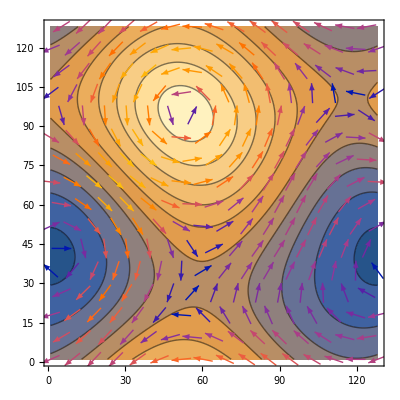

```mathematica
fftID2=Table[-1/(x^2+y^2)/.ComplexInfinity->0,{x,0,128-1},{y,0,128-1}];
fftDx=Table[I x,{x,0,128-1},{y,0,128-1}];
fftDy=Table[I y,{x,0,128-1},{y,0,128-1}];
streamFuncDiscrete[ex_]:=Transpose@Re@InverseFourier[-fftID2 Fourier[Re@InverseFourier[Fourier[ex[[;;,;;,2]]] fftDx]-Re@InverseFourier[Fourier[ex[[;;,;;,1]]] fftDy]]]
ListPlot3D@streamFuncDiscrete[limitedExamples[[15]]]
skewDiscrete[l_]:=Map[{-#[[2]],#[[1]]}&,l,{2}];
discreteToInterp[dis_]:=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}][Mod[x,2Pi],Mod[y,2Pi]];
homologyPlot[discreteToInterp[streamFuncDiscrete[limitedExamples[[15]]]]]
Show[ListContourPlot[streamFuncDiscrete[limitedExamples[[15]]]],ListVectorPlot[limitedExamples[[15]]]]
```

Max  {4.64489,2.59679,136.835}

Min  {1.96311,0.000882114,-106.236}

Saddle 1  {1.68074,2.73564,-3.8993}

Saddle 2  {4.77131,6.08117,-0.972773}

-Graphics3D-

NDSolveValue::ndnco: The number of constraints (6) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (8).

NDSolveValue[{{px'[t],py'[t]}=={(1-(Piecewise[{{0, px[t]/(2 π)>Floor[px[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]],(1-(Piecewise[{{0, py[t]/(2 π)>Floor[py[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]]}},{px[t],py[t]},{t,0,1}]

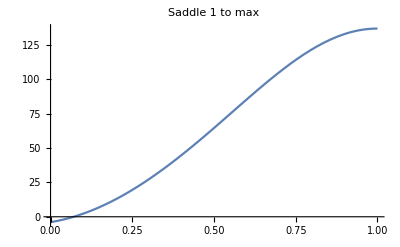

{205.71,100.266,-1546.52,219.244}

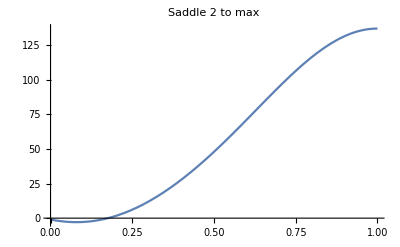

{219.523,312.389,-1706.52,-652.316}

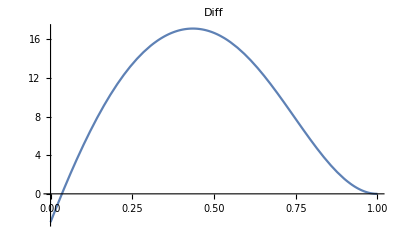

Max  {2.83107,2.29022,133.982}

Min  {0.0603587,5.78648,-133.564}

Saddle 1  {3.14739,5.65797,-16.7318}

FindMinimum::acceptlev: Solved to acceptable level.

Saddle 2  {6.15345,2.37916,8.41331}

-Graphics3D-

NDSolveValue::ndnco: The number of constraints (6) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (8).

NDSolveValue[{{px'[t],py'[t]}=={(1-(Piecewise[{{0, px[t]/(2 π)>Floor[px[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]],(1-(Piecewise[{{0, py[t]/(2 π)>Floor[py[t]/(2 π)]}, {Indeterminate, True}}])) InterpolatingFunction[…][Mod[px[t],2 π],Mod[py[t],2 π]]}},{px[t],py[t]},{t,0,1}]

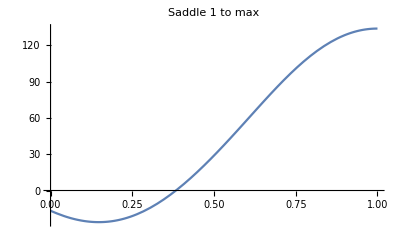

{277.519,391.083,-2875.73,-796.5}

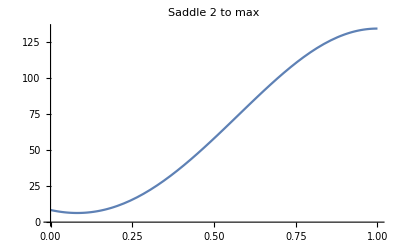

{212.51,174.413,-2269.,-555.78}

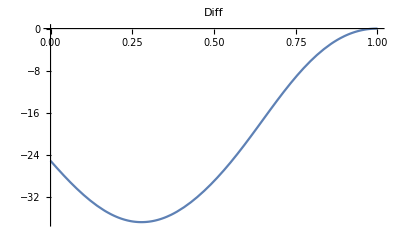

```mathematica
exhibit[n_,seeds_]:=Module[{},
exampleStreamFunc=discreteToInterp[streamFuncDiscrete[limitedExamples[[n]]]];
absMax={Mod[x,2Pi],Mod[y,2Pi],exampleStreamFunc}/.FindMaximum[{exampleStreamFunc,{x,y}∈extDomain},{{x,seeds[[1,1]]},{y,seeds[[1,2]]}}][[2]]//EchoLabel["Max"];
absMin={Mod[x,2Pi],Mod[y,2Pi],exampleStreamFunc}/.FindMinimum[{exampleStreamFunc,{x,y}∈extDomain},{{x,seeds[[2,1]]},{y,seeds[[2,2]]}}][[2]]//EchoLabel["Min"];
saddle1={Mod[x,2Pi],Mod[y,2Pi],exampleStreamFunc}/.FindMinimum[{discreteToInterp[discreteHessdet@streamFuncDiscrete@limitedExamples[[n]]],{x,y}∈extDomain},{{x,seeds[[3,1]]},{y,seeds[[3,2]]}}][[2]]//EchoLabel["Saddle 1"];
saddle2={Mod[x,2Pi],Mod[y,2Pi],exampleStreamFunc}/.FindMinimum[{discreteToInterp[discreteHessdet@streamFuncDiscrete@limitedExamples[[n]]],{x,y}∈extDomain},{{x,seeds[[4,1]]},{y,seeds[[4,2]]}}][[2]]//EchoLabel["Saddle 2"];
Show[Plot3D[exampleStreamFunc,{x,y}∈dom,PlotLabel->StringForm["n=``",n]],ListPointPlot3D[{absMax->"Max",absMin->"Min",saddle1->"Saddle 1",saddle2->"Saddle 2"},PlotStyle->PointSize[0.1]]]//Print;
NDSolveValue[{D[{px[t],py[t]},t]==Grad[exampleStreamFunc,{x,y}]/.{x->px[t],y->py[t]}},{px[t],py[t]},{t,0,1}]//Print;
funcSad1[t_]=exampleStreamFunc/.{x->saddle1[[1]](1-t)+absMax[[1]]t,y->saddle1[[2]](1-t)+absMax[[2]]t};
funcSad2[t_]=exampleStreamFunc/.{x->saddle2[[1]](1-t)+absMax[[1]]t,y->saddle2[[2]](1-t)+absMax[[2]]t};
Plot[funcSad1[t],{t,0,1},PlotLabel->"Saddle 1 to max"]//Print;
Table[D[funcSad1[t],{t,o}],{o,1,4}]/.t->0.5//Print;
Plot[funcSad2[t],{t,0,1},PlotLabel->"Saddle 2 to max"]//Print;
Table[D[funcSad2[t],{t,o}],{o,1,4}]/.t->0.5//Print;
Plot[funcSad1[t]-funcSad2[t],{t,0,1},PlotLabel->"Diff"]//Print;
]
exhibit[15,{{2,6},{2,6},{1,4},{5,6}}]
exhibit[50,{{2,2},{5,6},{3,4},{6,2}}]
```

Max  {5.86965,2.59331,130.207}

Min  {2.70263,5.67338,-110.244}

Saddle 1  {2.66533,2.53259,33.6841}

Saddle 2  {5.45001,5.41358,-43.7075}

-Graphics3D-

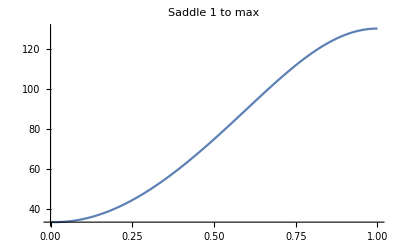

{145.945,124.219,-995.526,-260.491}

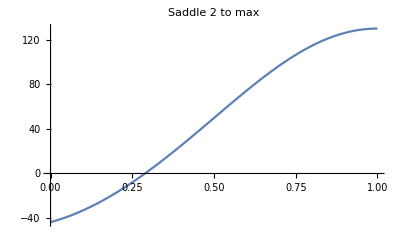

{249.923,2.45771,-2121.66,725.81}

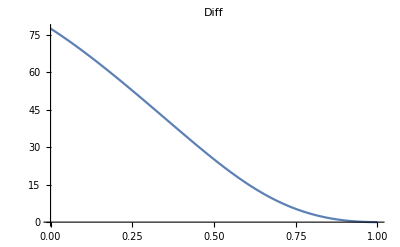

```mathematica
exhibit[70,{{2,2},{5,6},{3,4},{6,2}}]
```

```mathematica
ParametricPlot3D[{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{u,0,2Pi},{v,0,2Pi}]
torusRegion=ParametricRegion[{{4+(3+Cos[y]) Sin[x],4+(3+Cos[y]) Cos[x],4+Sin[y]},exampleStreamFunc<0},{{x,0,2Pi},{y,0,2Pi}}]
(*%//DiscretizeRegion
%//ConnectedMeshComponents*)
```

-Graphics3D-

ParametricRegion[{{4+(3+Cos[y]) Sin[x],4+Cos[x] (3+Cos[y]),4+Sin[y]},InterpolatingFunction[…][x,y]<0&&0≤x≤2 π&&0≤y≤2 π},{x,y}]

ImplicitRegion[InterpolatingFunction[…][x,y]<0&&0≤x≤2 π&&0≤y≤2 π,{x,y}]

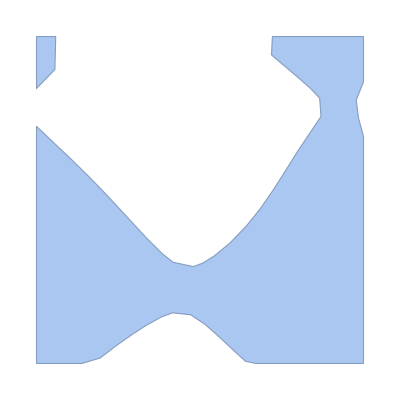

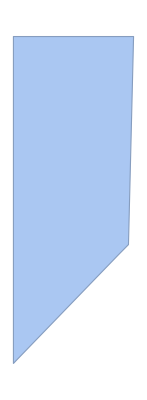
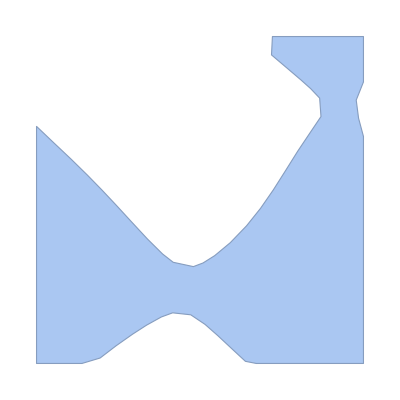

```mathematica
ImplicitRegion[exampleStreamFunc<0,{{x,0,2Pi},{y,0,2Pi}}]
%//BoundaryDiscretizeRegion
%//ConnectedMeshComponents
```

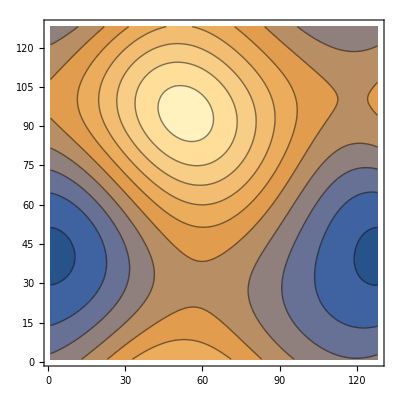

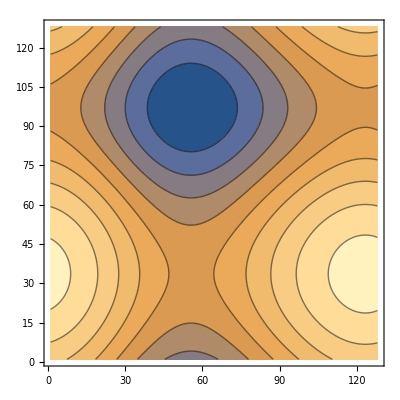

```mathematica
discreteHessxx[xs_]:=Re@InverseFourier[Fourier[xs](fftDx fftDx)]
discreteHessyy[xs_]:=Re@InverseFourier[Fourier[xs](fftDy fftDy)]
discreteHessxy[xs_]:=Re@InverseFourier[Fourier[xs](fftDx fftDy)]
discreteHessdet[xs_]:=discreteHessxx[xs]discreteHessyy[xs]-2discreteHessxy[xs]
ListContourPlot@streamFuncDiscrete[limitedExamples[[15]]]
ListContourPlot@discreteJacobian[streamFuncDiscrete[limitedExamples[[15]]]]
```

```mathematica
frames=ParallelMap[Image[ListContourPlot[streamFuncDiscrete@#,PerformanceGoal->"Speed",ColorFunction->"TemperatureMap"],ImageSize->Large]&,limitedExamples];
```

```mathematica
Export["chargeDynamics.gif",frames,"AnimationRepetitions"->∞]
```

chargeDynamics.gif